```mathematica
x[r_,th_]:=r Cos[th]
y= r Sin[th]
```

1.5 Tan[th]

```mathematica
a=1.5;
```

```mathematica
r=a/Cos[th];
```

```mathematica
x[r,th]
```

1.5

```mathematica
p1=PolarPlot[{-a/Cos[th],a/Cos[th]},{th,-π/4,π/4},PlotStyle->Blue];
```

```mathematica
p2=PolarPlot[{-a/Sin[th],a/Sin[th]},{th,π/4,(3π)/4},PlotStyle->Orange];
```

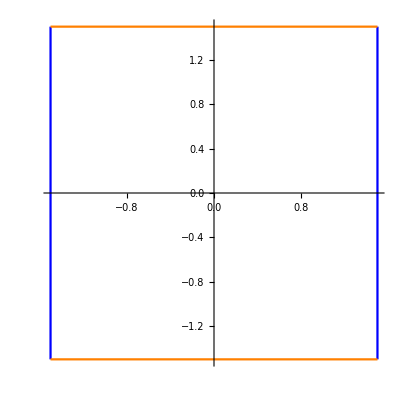

```mathematica
Show[p1,p2]
```

```mathematica
(*2D*)
```

```mathematica
Integrate[x1^2*y1^2,{x1,-1,1},{y1,-1,1}]
```

4/9

```mathematica
expr=Integrate[(r1 Cos[th1])^2*(r1 Sin[th1])^2 r1,{th1,0,π/4},{r1,0,Sqrt[2]/Cos[th1]}]
```

4/9

```mathematica
Integrate[(Cos[th1])^2*(Sin[th1])^2 (Sqrt[2]/Cos[th1])^6/6,{th1,0,π/4}]
```

4/9

```mathematica
(*3D*)
```

```mathematica
Integrate[x1^2*y1^2*z1^2,{x1,-1,1},{y1,-1,1},{z1,-1,1}]
```

8/27

```mathematica
Integrate[(r1 Cos[th1])^2*(r1 Sin[th1] )^2*z1^2 * r1,{th1,0,π/4},{z1,-1,1},{r1,0,Sqrt[2]/Cos[th1]}]
```

8/27

```mathematica
(1^3/3+1^3/3)Integrate[(Cos[th1])^2*(Sin[th1] )^2 * (Sqrt[2]/Cos[th1])^6/6,{th1,0,π/4}]
```

8/27

```mathematica
r = a/(Cos[ph]Sin[th])
```

1.5 Csc[th] Sec[ph]

```mathematica
r = a/(Sin[ph]Sin[th])
```

1.5 Csc[ph] Csc[th]

```mathematica
r = a/Cos[th]
```

1.5 Sec[th]

```mathematica
ArcCos[1/Sqrt[3]]//N
```

0.955317

```mathematica
ArcCos[-1/Sqrt[3]]//N
```

2.18628

```mathematica
ArcTan[1]
```

π/4

```mathematica
ArcTan[-1]
```

-π/4

```mathematica
ArcTan[(-Sqrt[2])/1]//N
```

-0.955317

```mathematica
SphericalPlot3D[1/(Cos[ph]Sin[th]),{th,π/3,π/2},{ph,-π/4,π/4}]
```

-Graphics3D-